```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

Load pre-processed data

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"]
```

#### Setup

```mathematica
edgeTension[cellPair_,t_]:=If[
MissingQ[#],#,
quartetEdgeTension[#[[4]]]
]&@edgeNeighborProperties[cellPair,t]
```

```mathematica
edgeTensionFallback[cellPair_,t_]:=With[{res=edgeNeighborProperties[cellPair,t]},
If[MatchQ[res,Missing["DegenerateVertex",_]],
If[t>=2,
edgeTensionFallback[cellPair,t-1],
res
],
If[MissingQ[res],
res,
quartetEdgeTension[res⟦4⟧]
]
]
]
```

```mathematica
blueRedBlend[x_]:=Blend[{RGBColor[0,0,0.9],GrayLevel[0.8],RGBColor[0.9,0,0]},x]
```

```mathematica
blueRedBlend/@Range[0,1,0.1]
```

{RGBColor[0., 0., 0.9],RGBColor[0.16000000000000003, 0.16000000000000003, 0.88],RGBColor[0.32000000000000006, 0.32000000000000006, 0.86],RGBColor[0.4800000000000001, 0.4800000000000001, 0.8400000000000001],RGBColor[0.6400000000000001, 0.6400000000000001, 0.8200000000000001],RGBColor[0.8, 0.8, 0.8],RGBColor[0.8200000000000001, 0.6399999999999999, 0.6399999999999999],RGBColor[0.8400000000000001, 0.4799999999999999, 0.4799999999999999],RGBColor[0.8600000000000001, 0.31999999999999995, 0.31999999999999995],RGBColor[0.88, 0.15999999999999992, 0.15999999999999992],RGBColor[0.9, 0., 0.]}

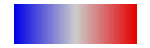

```mathematica
colorBar=ArrayPlot[{Range[0,1,0.01]},ColorFunction->blueRedBlend,AspectRatio->1/10,
PlotRangePadding->None,DataRange->{{0,2},{0,1}},
FrameTicks->{{None,None},{{0,1,2},None}},FrameTicksStyle->Black,
FrameLabel->{{None,Style["Relative tension",16]},{None,None}},
BaseStyle->{Black,14},FrameStyle->Black,
ImageSize->150
]
```

#### Render germ band patch movie

Select patch cells for rendering

```mathematica
selectedCells=getNeighborhood[12566,100,4]
```

{6153,6184,6226,6255,6293,6301,6336,6342,6373,6387,6398,6414,6425,6449,6479,6480,6502,6515,6542,6543,6558,6578,6609,6621,6634,6653,6654,6672,6702,6707,6721,6747,6755,6791,6836,12225,12258,12290,12316,12325,12336,12372,12373,12385,12414,12424,12440,12463,12479,12505,12509,12510,12550,12564,12565,12566,12583,12601,12634,12655,12672,12675,12676,12698,12755,12766,12786,12834,12864,12877,12890}

```mathematica
renderFrame[t_,timestamp_:True]:=Module[{edges,tensions,com,tension},
com=Mean[toCylinder[cellCentroidsTS[[t]][#]]&/@selectedCells];
edges=Union[Sort/@Catenate[
Thread[{#,Intersection[cellNeighborsTS[[t]][#],selectedCells]}]&/@selectedCells]];
Graphics[{
If[timestamp,
Text[Style["t = "<>ToString[IntegerString[Round[(t-1)/4.]]]<>" min",16],com+{-50,40},{-1,-1}]
],
(*Inset[colorBar,Scaled[{0.8,0.15}]],*)
AbsoluteThickness[3],
EdgeForm[Gray],FaceForm[GrayLevel[0.95]],
renderCell2D[#,t]&/@selectedCells,
Function[edge,
tension=edgeTensionFallback[edge,t];
If[!MissingQ[tension],
{
blueRedBlend[tension/2],
Line[toCylinder@vertexCoordsTS[[t,sharedVertices[edge,t]]]]
}]
]/@edges
},
PlotRange->({com[[1]]+{-60,60},com[[2]]+{-50,50}}),
Background->White,
ImageSize->500
]
]
```

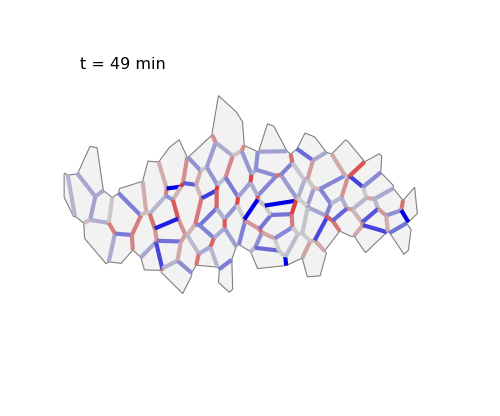

```mathematica
renderFrame[198]
```

### Render small ROIs for Fig 2C, C’

#### Germ band

```mathematica
selectedCells=getNeighborhood[6542,100,3]
```

{6301,6342,6373,6387,6398,6425,6449,6479,6502,6515,6542,6543,6578,6609,6621,6653,6654,6672,6702,6747,6755,6791,6836,12385,12414,12440,12479,12505,12550,12565,12566,12601,12655,12676,12698,12766,12786,12864,12890}

```mathematica
inFrame[p_,{{x0_,x1_},{y0_,y1_}}]:=x0<p[[1]]<x1&&y0<p[[2]]<y1
```

```mathematica
ClearAll[renderFrame];
renderFrame[t_]:=Module[{cells,edges,tensions,com,tension},
com=Mean[toCylinder[cellCentroidsTS[[t]][#]]&/@selectedCells];
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#],{com[[1]]+{-25,25},com[[2]]+{-25,25}}]&
]];
edges=Union[Sort/@Catenate[Thread[{#,cellNeighborsTS[[t]][#]}]&/@cells]];
Graphics[{
FaceForm[GrayLevel[0.95]],EdgeForm[None],
renderCell2D[#,t,"Tooltip"]&/@{6609,6542,6653,12655},
AbsoluteThickness[3],CapForm["Round"],
Function[edge,
tension=edgeTensionFallback[edge,t];
{
ReleaseHold@If[!MissingQ[tension],
(*ColorData["Rainbow"][tension/2],*)
Hold[Sequence[AbsoluteThickness[3.5 √Clip[tension,{0,2}]],blueRedBlend[tension/2]]],
Hold@Sequence[AbsoluteThickness[1],Gray]
],
Line[toCylinder@vertexCoordsTS[[t,sharedVertices[edge,t]]]]
}
]/@SortBy[edges,-Norm[#[[1]]-#[[2]]&@vertexCoordsTS[[t,sharedVertices[#,t]]]]&]
},
PlotRange->{com[[1]]+{-20,20},com[[2]]+{-20,20}},
Background->GrayLevel[1],
ImageSize->200
]
]
```

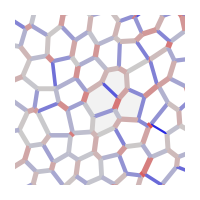
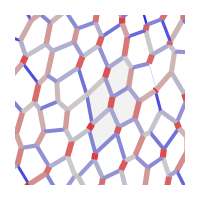
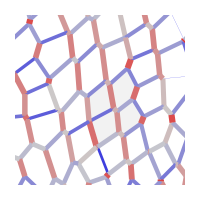
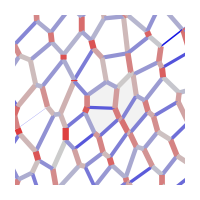

```mathematica
renderFrame/@{2,89,121,150}
```

#### Amnioserossa (dorsal)

```mathematica
selectedCells=Select[Keys[cellCentroidsTS[[1]]],210<#[[1]]<260&&(#[[2]]>530||#[[2]]<10)&@toCylinder[cellCentroidsTS[[1]][#]]&];
```

```mathematica
ClearAll[renderFrame];
renderFrame[t_]:=Module[{cells,edges,tensions,com,tension},
com=Mean[toCylinder[cellCentroidsTS[[t]][#],Offset->0]&/@Intersection[selectedCells,Keys[cellCentroidsTS[[t]]]]];
cells=Keys[Select[
cellCentroidsTS[[t]],
inFrame[toCylinder[#,Offset->0],{com[[1]]+{-25,25},com[[2]]+{-25,25}}]&
]];
edges=Union[Sort/@Catenate[Thread[{#,cellNeighborsTS[[t]][#]}]&/@cells]];
Graphics[{
FaceForm[GrayLevel[0.9]],EdgeForm[None],
renderCell2D[#,t,Offset->0]&/@{6779,6866,6774,6703},
AbsoluteThickness[3],
Function[edge,
tension=edgeTensionFallback[edge,t];
{
ReleaseHold@If[!MissingQ[tension],
Hold[Sequence[AbsoluteThickness[3.5 √Clip[tension,{0,2}]],blueRedBlend[tension/2]]],
Hold@Sequence[AbsoluteThickness[1],Gray]
],
Line[toCylinder[vertexCoordsTS[[t,sharedVertices[edge,t]]],Offset->0]]
}
]/@SortBy[edges,-Norm[#[[1]]-#[[2]]&@vertexCoordsTS[[t,sharedVertices[#,t]]]]&]
},
PlotRange->{com[[1]]+{-20,20},com[[2]]+{-20,20}},
Background->GrayLevel[1],
ImageSize->200
]
]
```

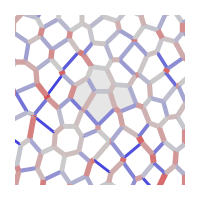
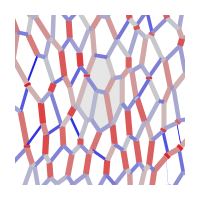
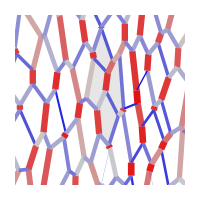
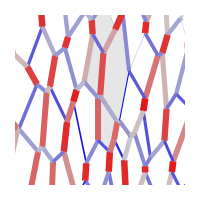

```mathematica
renderFrame/@{1,115,134,151}
```